```mathematica
Needs["GraphUtilities`"]
j =AdjacencyGraph[{{1,0,0,0,1,1,0,1},{0,0,0,1,0,0,1,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,1,0,0},{1,0,0,1,1,1,0,1},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1},{1,0,1,0,0,1,0,0}}]
```

-Graphics-

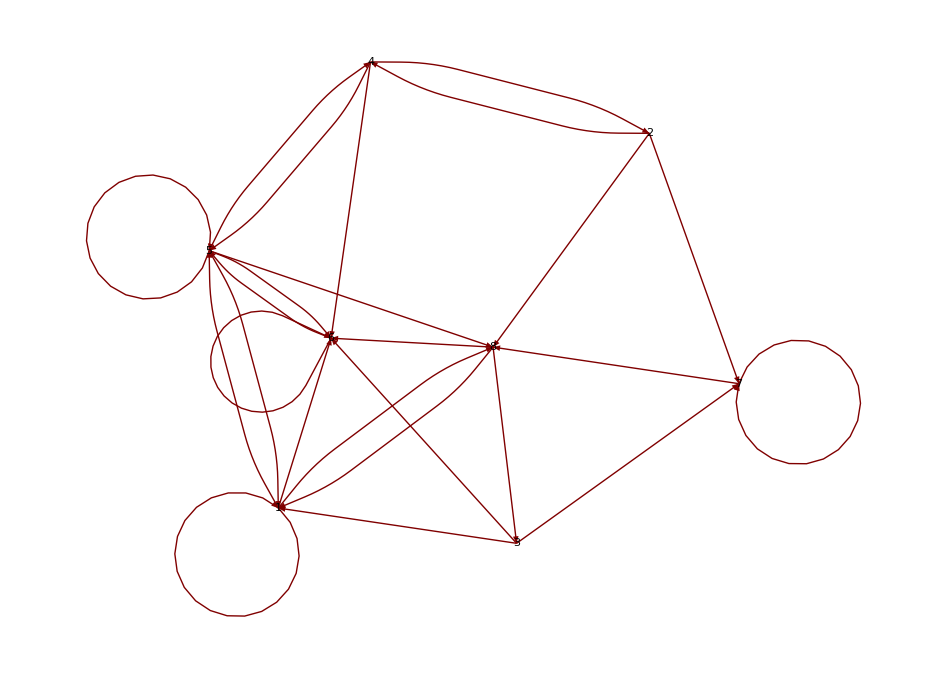

```mathematica
GraphPlot[j,VertexLabeling->True]
```

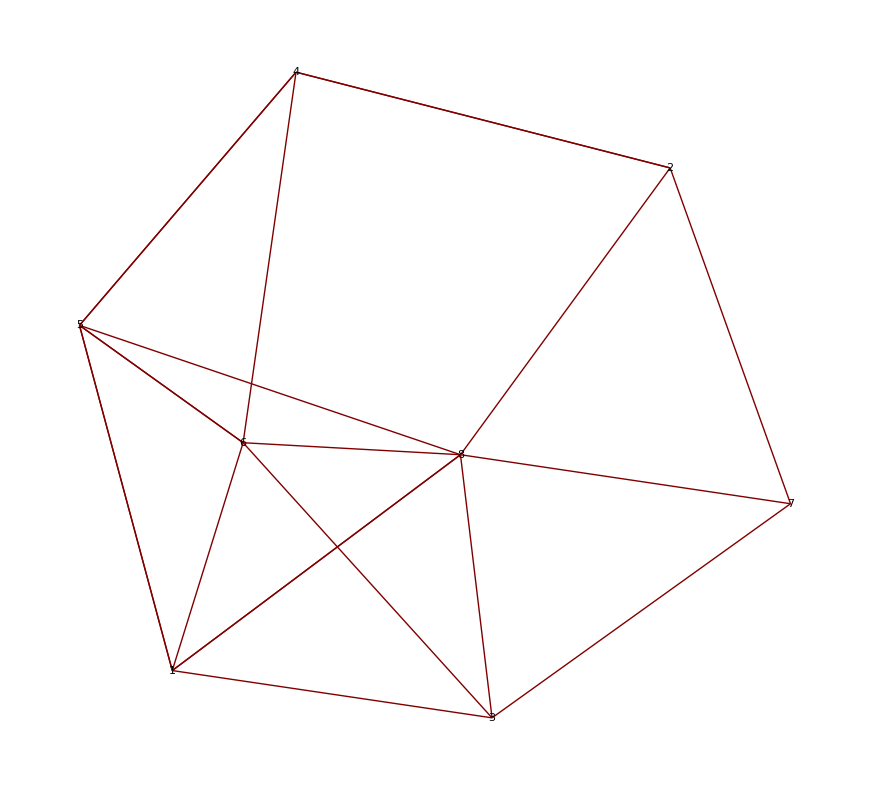

```mathematica
GraphPlot[j,VertexLabeling->True,DirectedEdges->False,SelfLoopStyle->False,MultiedgeStyle->False]
```

```mathematica
n =AdjacencyGraph[{{0,0,1,0,1,1,0,1},{0,0,0,1,0,0,1,1},{1,0,0,0,0,1,1,1},{0,1,0,0,1,1,0,0},{1,0,0,1,0,1,0,1},{1,0,1,1,1,0,0,1},{0,1,1,0,0,0,0,1},{1,1,1,0,1,1,1,0}},EdgeStyle->{5<->1->Dashed,7<->8->Dashed,2<->8->Dashed,4<->6->Dashed,1<->6->Dashed,1<->8->Dashed,3<->6->Dashed,3<->8->Dashed,6<->8->Dashed,1<->3->Thick,3<->7->Thick,7<->2->Thick,2<->4->Thick,4<->5->Thick,5<->6->Thick,5<->8->Thick}]
```